# Text Generation using GANs

Suman Sigdel

Bennington College

Goal : Generative Adversarial Networks have been used mostly for image data and are known to produce data that closely match the given input eg. deep fakes. Text generation is an area in which GANs are used less given the discrete structures of text. We believe that CNN based GAN architecture used for images can also be used in text generation to generate comparable results to that of RNN models. A comparison between GANs and RNNs will be made to draw a clear distinction between the results they produce using n-gram distributions as a performance metric. 

Results : Comparing the two text generation models, using euclidean distance of n-gram as a metric, we found that the text generated by the GAN model (for shorter lengths) is better than the RNN model for multiple n-grams. Although the unstable nature of GANs might affect it’s performance, we believe that through multiple fine tuning methods and proper model selection using the n-gram metric, the GAN model’s performance can be further improved.

Application : 
Text generation models can be used for :  product names, naming new chemicals, naming new startups etc.

## Wolfram Community Post (material for blog post)

Introduction
Generative Adversarial Networks or GANs are most commonly known to produce results that are almost indistinguishable from the real dataset eg. deep fakes. GANs consist of two neural networks, Generator and Discriminator which compete in an adversarial zero sum game in order to generate plausible examples. The generator never sees the actual training data and only gets data from a latent space, to which it assigns meaning with the help of the discriminator. The discriminator is trained with samples generated by the generator and the samples from the training dataset and learns to classify between real and fake data. The two models operate in a zero sum game in a sense that when the discriminator successfully classifies real and fake samples, it is rewarded with no updates made to the model parameters, however the generator is penalized with large updates. Similarly, when the generator generates plausible examples, only the discriminator’s parameters are updated. Large amounts of research have been done with GANs for image translation, generation of deep fakes and data augmentation, but GANs application in text and NLP is an area that is less explored.

Aim
In this project, I will be applying GANs for text generation and will be comparing the results with existing Recurrent Neural Networks. This project aims to show that through adversarial training better text generation results can be achieved which is comparable to existing RNN models. This post is divided into 4 sections. In the first section, I will explain the metric that will be used to measure the performance of the text generation models. I will then train existing RNN language model with chemical and company names and show it’s performance. I will then explain the GAN architecture that was used for text generation and will show it’s performance while generating texts and finally will make a comparison between the performance of GAN and RNN model.

## 1. Performance Metric

Normalizing text

To compare the different model performances, we will be finding the euclidean distance of n-grams between text generated from two models. The initial step will be to remove special characters and diacritics from the real dataset. The following code accomplishes this goal by using a combination of StringReplace, ToLowerCase and Remove Diacritics functions to normalize the characters in the dataset.

```mathematica
normalizeText[s_] := ToLowerCase @ RemoveDiacritics @ StringReplace[s,
	{WordBoundary~~(WordCharacter..)~~".":>"",(*Remove "mr.","jr.",...*)
	"♂"|"♀"->"",(*Remove gender hints*)
	"-"|"-"|"'"->" ",(*Remove very rare characters*)
	DigitCharacter->"" ,(*Remove very rare characters*)
	"("|")" -> "",(*Remove Brackets*)
	"%"|":" -> "",(*Remove Colons and %*)
	"ʻ" |"‘"->  "",(*Remove other special characters*)
	"`"->"",
	" " -> "",
	"="|"?"->"",
	"}"|"{"-> ""}
]
```

Computing n-grams

The next step is to create a lookup table for the different characters so that we can put them in their respective coordinates in the sparse array. The following code makes an association that maps characters and special tokens to an unique point.

```mathematica
characters = AssociationThread[
	Join[CharacterRange["a","z"], {" ", StartOfString, EndOfString}]
	-> Range[29]];
```

A function to compute n-grams is created which computes n-gram for a given wordlist and puts frequencies of each n-gram in a SparseArray. A sparse-array is chosen for faster computation for higher “n” in the n-grams.

```mathematica
computeNGrams[texts_, n_] := Block[{ngrams},
	ngrams = Flatten[
		Function[Partition[#, n, 1]] /@ 
		Function[Join[{StartOfString}, Characters[#], {EndOfString}]] /@ normalizeText[texts],
		1
	];
	(* Convert to indices *)
	ngrams = Map[Lookup[characters, #]&, ngrams];
	(* Counts *)
	ngrams = Normal[N @ Counts[ngrams] / Length[ngrams]];
	(* Fill SparseArray *)
	SparseArray[ngrams, Table[Length[characters],n]]
];
```

Example

Running the following code will normalize chemical names.

```mathematica
chemicalNames = EntityValue[EntityList["Chemical"],"Name"];
chemicalNames = Select[c,StringMatchQ[#,CharacterRange["A","z"]..]&];
tennormalizednames = Take[normalizeText@chemicalNames,10]
```

{hydrogen,helium,deuterium,lithium,beryllium,boron,diamond,graphite,borane,methane}

The following code will then compute the 1 and 2 grams and map their indices to respective normalized occurrences in a SparseArray.

```mathematica
computeNGrams[tennames,1]
computeNGrams[tennames,2]
```

SparseArray[…]

SparseArray[…]

Euclidean Distance between n-gram distributions

We then compute the euclidean distance between the distributions of n-grams in the dataset and generated text. The findEuclideanDistance computes the euclidean distance between two n gram distributions. The DistancesofNgrams function takes the generator and the training dataset to find the euclidean distance between n-gram distributions (between generated and training dataset) where n goes from 1 to 5.

```mathematica
findEuclideanDistance[ngram1_,ngram2_]:= EuclideanDistance[Flatten@ngram1,Flatten@ngram2]

DistancesofNgrams[generator_, dataset_]:= Table[findEuclideanDistance[computeNGrams[generator@latentGeneration[1000],n], computeNGrams[dataset,n]],{n,1,5}]
```

Using this metric we will be able to compare the GAN model as well as the RNN model. In addition, we will be able to see how the euclidean distance converges as the GAN model is trained.

## ( Murgue T., de la Higuera C. (2004) Distances between Distributions: Comparing Language Models. In: Fred A., Caelli T.M., Duin R.P.W., Campilho A.C., de Ridder D. (eds) Structural, Syntactic, and Statistical Pattern Recognition. SSPR /SPR 2004. Lecture Notes in Computer Science, vol 3138. Springer, Berlin, Heidelberg)

## 2. RNN Model The RNN model that will be used for comparison is the pretrained "Wolfram English Character-Level Language Model V1". https://resources.wolframcloud.com/NeuralNetRepository/resources/Wolfram-English-Character-Level-Language-Model-V1#:~:text=This%20language%20model%20is%20based,on%20sequences%20of%20length%2080.Nonehttps://resources.wolframcloud.com/NeuralNetRepository/resources/Wolfram-English-Character-Level-Language-Model-V1#:~:text=This%20language%20model%20is%20based,on%20sequences%20of%20length%2080.HyperlinkActionRecycledHyperlinkActiveThe following is the architecture of this model :

```mathematica
NetModel["Wolfram English Character-Level Language Model V1"]
```

NetChain[<>]

We will now train the RNN model on 3 different datasets and measure their respective euclidean distance for 1 to 5 n-grams.

### 1. Chemical Names

The following code gets the chemical names from the EntityList and normalizes the names. The pretrained model is trained with the normalized chemical names with the default hyperparameters.

```mathematica
chemicalNames= EntityValue[EntityList["Chemical"],"Name"];
chemicalNames = Select[chemicalNames,StringMatchQ[#,CharacterRange["A","z"]..]&];
normalizedChemicalNames = normalizeText@chemicalNames;
```

```mathematica
chemicalRNN = Import["/Users/sumansigdel/ChemicalRNN.wlnet"];
Chemicalnet=NetReplacePart[NetExtract[chemicalRNN,"predict"],{"Input"->NetEncoder[{"Characters",{vocabulary,EndOfString},"TargetLength"->1}],"Output"->NetDecoder[{"Class",Append[vocabulary,""]}]}];
randomChemical[]:=With[{obj=NetStateObject[Chemicalnet]},StringJoin@NestWhileList[obj[Last[#],"RandomSample"]&,Sequence[{"",""},#=!={""}&,1,100]]];
newChemicals=Sort@Complement[Table[randomChemical[],5000], normalizedChemicalNames];
```

Here are some chemical names that were generated by the RNN model.

```mathematica
RandomChoice[newChemicals,10]
```

{dopaquinox,lecalein,esopiulfon,methiocarbazide,bitosnan,mephoxybenzone,hexyldimethyloctylsilane,spiropentylbenzene,damuscinol,tetrachlorocyclodecane}

The performance of the RNN model is now calculated using the performance metric of euclidean distance between the n-grams.

```mathematica
ChemicalNamesDistancesRNN= Table[findEuclideanDistance[computeNGrams[newChemicals,n], computeNGrams[normalizedChemicalNames,n]],{n,1,5}]
```

{0.0129824,0.0123536,0.0120765,0.0122143,0.0126008}

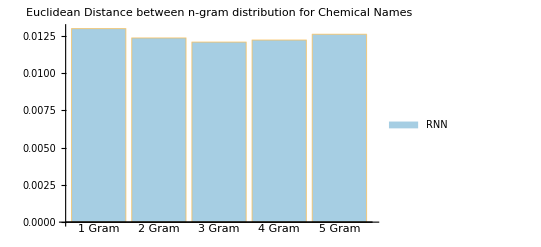

```mathematica
BarChart[ChemicalNamesDistancesRNN,ChartLabels->{"1 Gram","2 Gram","3 Gram","4 Gram","5 Gram"}, ChartLegends->{"RNN"},PlotLabel->"Euclidean Distance between n-gram distribution for Chemical Names",ChartStyle->{RGBColor["#a6cee3"]}]
```

In the above bar chart, we see that the euclidean distance for all the 1-5 n-grams are quite close to the actual dataset. In addition, the example that were generated from the RNN are also plausible examples.

### 2. Company Names

The same RNN model will now be trained with company names taken from Kaggle. The dataset contains over 7 million names and for the training we will only take names of companies that have string length of 6 or less. The following are some company names from the dataset

```mathematica
Take[normalizedShortCompaniesList,10]
```

{ibm,ey,att,pwc,citi,amazon,apple,oracle,nokia,hsbc}

```mathematica
normalizedShortCompaniesList = normalizeText@Select[Flatten@dataset, StringLength[#] ≤6 &];
Take[normalizedShortCompaniesList,10]
```

{ibm,us army,ey,walmart,att,pwc,infosys,deloitte,citi,us navy}

Training the pretrained character level RNN on the company names dataset.

```mathematica
CompanyNamesnet=NetReplacePart[net,"Input"->NetEncoder[{"Characters",{vocabulary,{StartOfString,EndOfString}->97}}]]
```

```mathematica
CompanyNamesresults=NetTrain[CompanyNamesnet,<|"Input"->normalizedShortCompaniesList|>,All,LossFunction->"Loss",MaxTrainingRounds->100]
```

NetGraph[<>]

Upon running the RNN model, the following examples were produced and the euclidean distance is calculated as per the performance metric.

```mathematica
generatedCompany=Sort@Complement[Table[randomGeneratedCompany[],1000],normalizedShortCompaniesList];
Take[generatedCompany,10]
```

{aamp,aasu,aceic,acmas,acolux,actain,acws,adayi,addpowar,adio}

```mathematica
CompanyNamesDistancesRNN =Table[findEuclideanDistance[computeNGrams[generatedCompany,n], computeNGrams[SeedRandom[1234];RandomChoice[normalizedShortCompaniesList,1000],n]],{n,1,5}]
```

{0.0249101,0.0220684,0.0220686,0.0239113,0.027024}

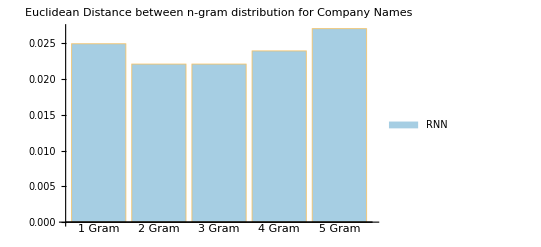

```mathematica
BarChart[CompanyNamesDistancesRNN,ChartLabels->{"1 Gram","2 Gram","3 Gram","4 Gram","5 Gram"}, ChartLegends->{"RNN"},PlotLabel->"Euclidean Distance between n-gram distribution for Company Names",ChartStyle->{RGBColor["#a6cee3"]}]
```

## 3. GANs for text generation

Generative Adversarial Networks or GANs are a deep learning architecture for training generative models in which two models (Generator and Discriminator) train in an adversarial zero sum game. After training
the generator is able to produce plausible example that are almost indistinguishable from the training set data. Recent improvements in GANs have significantly improved data augmentation in machine learning tasks that deal with images and in this section of the post some changes to a GAN architecture will be made in order for text generation. Similar to GANs used for images, the following models make use of Convolutional Blocks comprised of batch normalization, a Leaky ReLU non-linearity with an alpha of 0.2 and a dropout layer. I will begin by introducing the architecture for Discriminator and Generator and I will then train the composite GAN model on the same chemical names and company names and use the performance metric to get results for comparison.

Discriminator Model

The discriminator model is a binary classification model which simply differentiates if the data fed to the model is real (from the training data) or fake (from the generator). Initially we take the max values from the provided matrix, taking only the max values has no effect on the  real samples matrix, however, it helps remove noise from the generator’s output matrix.  Similar to GANs used for images, the following discriminator model makes use of Convolutional Blocks comprised of batch normalization, a Leaky ReLU non-linearity with an alpha of 0.2 and a dropout layer. The output layer is a LogisticSigmoid which gives us the probability of a text being real or fake.

```mathematica
discriminator=NetChain[<|"keep max only"->NetGraph[{AggregationLayer[Max,-1],ThreadingLayer[If[#1≥#2-1.*^-7,#1,0]&,-1]},{{NetPort["Input"],1}->2}],Sequence@@Table["conv."<>ToString[i]->convolutionBlock[$numhiddens],{i,$depth}],"aggregate"->AggregationLayer[Mean,1],"dropout"->DropoutLayer[],"classify"->LinearLayer["Real","Weights"->0,"Biases"->None],If[$jensen,"logit"->LogisticSigmoid,Nothing]|>,"Input"->{"Varying",Length[characters2]}]
```

NetChain[<>]

Generator Model

The generator model is used to generate plausible examples from a vector that is randomly drawn from a gaussian distribution. During the training, the generator assigns meaning to the vector and outputs examples similar to the training set . The generator is dependent on discriminator for its updates; better performance of discriminator results in more updates to the generator and vice versa . The generator model has several hyperparameters like the latent dimension, non-linearity and normalization which will be used for fine-tuning the model for better performance. The last layer of this model is a softmax layer which gives us the probability of each character occurring and this can be used in the decoder to turn probabilities into text.

```mathematica
generator=NetChain[<|If[$generatorTerminalTokensQ,(*Append/Prepend EOS/SOS latent vectors*)"add eos/sos latent"->NetGraph[{ArrayLayer[],AppendLayer[],ArrayLayer[],PrependLayer[]},{{NetPort["Input"],1}->2,{2,3}->4}],Nothing],(*Core deep net*)Sequence@@Table["conv."<>ToString[i]->convolutionBlock[$numhiddens],{i,$depth}],If[$generatorTerminalTokensQ,(*Remove EOS/SOS high level features*)"remove eos/sos prediction"->NetChain[{SequenceRestLayer[],SequenceMostLayer[]}],Nothing],(*Classifier (of characters)*)"classify"->NetMapOperator@LinearLayer[Length[characters](*,"Weights"->0*)],"squash"->SoftmaxLayer[],If[$discriminatorTerminalTokensQ,"add eos/sos onehot proba"->NetGraph[{(*Catenate zero proba for EOS/SOS inside the generated text*)PaddingLayer[{{0,0},{0,2}}],(*Append/Prepend proba of 1 for EOS/SOS at the end/beginning of the generated text (to be in accordance with the discriminator)*)ArrayLayer["Array"->UnitVector[Length[characters2],Length[characters2]-1],LearningRateMultipliers->None],PrependLayer[],ArrayLayer["Array"->UnitVector[Length[characters2],Length[characters2]],LearningRateMultipliers->None],AppendLayer[]},{{1,2}->3,{3,4}->5}],Nothing]|>,"Input"->{"n",$numlatent},"Output"->With[{netpostproc=NetDecoder[netpreproc]},(*Capitalize the decoded (lower-case) text*)NetDecoder[{"Function",Function[StringReplace[netpostproc[#],WordBoundary~~c:WordCharacter:>ToUpperCase[c]]]}]]]
```

NetChain[<>]

```mathematica
Composite GAN Model
```

Wolfram Language contains a NetGANOperator to make a composite GAN model that takes generator and discriminator.

```mathematica
gan=NetGANOperator[{generator,discriminator}]
```

NetGANOperator[<>]

```mathematica
Training the model
```

It was found that the model performs better when the discriminator is updated twice as much as the generator. This makes significant updates to the generator in every epoch and also reduces the training time. In the NetTrain a data generator function is supplied which contains “sample” generation and “latent” vector generation.

Model Selection
GANs are very unstable during training as there are two networks that are dependent on each other for improvements in their performance. While several methods to improve the stability were implemented in the GAN architecture, they still suffer from non-convergence. Due to their unstable nature, an early stopping method fails to retrieve the best performing GAN model. In order to solve this, we will save a checkpoint of the model in every round along with the n-gram performance metric to select the best performing model.

```mathematica
dataGenerator={Function[<|"Sample"->sampleGeneration[#BatchSize],"Latent"->latentGeneration[#BatchSize]|>],"RoundLength"->Length[normalizedNames]};
```

```mathematica
NetTrain[gan,dataGenerator,TargetDevice->"GPU",BatchSize->$batchsize,TrainingUpdateSchedule->{"Discriminator","Discriminator","Generator"},MaxTrainingRounds->100000,
TrainingProgressFunction->{{Function@Block[{generator, ngramDistance},
generator=NetExtract[#Net,"Generator"];
ngramDistance =DistancesofNgrams[generator,normalizedNames];
Echo@ngramDistance;

],"Interval"->Quantity[10,"Rounds"]},

{
wssTrainingProgressFunction,
"Interval"->Quantity[10,"Rounds"]
}

},
TimeGoal->timeGoal
];
```

1. Chemical Names
The same dataset of chemical names was used to train the following GAN.

```mathematica
chemicalGAN = Import["/Users/sumansigdel/ChemicalGAN.wlnet"]
```

NetGANOperator[<>]

We will now extract the generator from the GAN model and feed the latent random given by the latent generation function.

```mathematica
latentGeneration[batchSize_]:=Table[Block[{len=Max[3,RandomChoice[Values[counts]->Keys[counts]]]},NumericArray[#,"Real32"]&@Clip[RandomVariate[NormalDistribution[],{len,16}],{-1,1}]],batchSize];
```

```mathematica
chemicalGenerator = NetExtract[chemicalGAN,"Generator"];
```

Here are 10 chemical names generated by the GAN.

```mathematica
chemicalGenerator@latentGeneration[10]
```

{Cephouromonazine,Cidenazine,Deropylltertine,Tramltne,Dinoamoldoxol,Metrexol,Flophabetrone,Poribeazene,Sulothlariyline,Macerminezone}

We now use the performance metric with the chemical names and plot a bar chart.

```mathematica
chemicalDistanceGAN = DistancesofNgrams[chemicalGenerator, normalizedChemicalNames]
```

{0.024628,0.0320187,0.0304281,0.0268123,0.0225618}

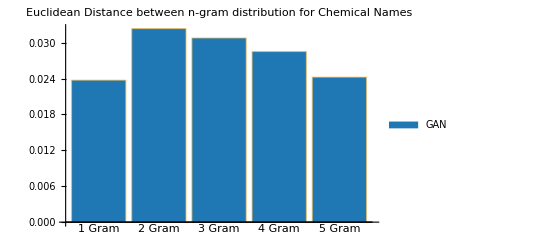

```mathematica
BarChart[chemicalGANDistance, ChartLegends->{"GAN"},ChartLabels->{"1 Gram","2 Gram","3 Gram","4 Gram","5 Gram"}, PlotLabel->"Euclidean Distance between n-gram distribution for Chemical Names",ChartStyle->{RGBColor["#1f78b4"]}]
```

```mathematica
2. Company Names
```

Similarly, we will now train another GAN model on company names of String Length less than or equal to 6. Upon evaluation of the n-gram metric during training in every 10 rounds there was not a significant change to the euclidean distances. A few tweaks were made to the GAN model. The latent dimension was reduced to 10 and the first convolutional layer of the generator had only 64 filters instead of 128.

```mathematica
companyGAN = Import["/Users/sumansigdel/CompanyGAN3rd.wlnet"]
```

NetGANOperator[<>]

```mathematica
latentGeneration[batchSize_]:=Table[Block[{len=Max[3,RandomChoice[Values[counts]->Keys[counts]]]},NumericArray[#,"Real32"]&@Clip[RandomVariate[NormalDistribution[],{len,10}],{-1,1}]],batchSize];
```

```mathematica
companyGenerator= NetExtract[companyGAN,"Generator"];
```

```mathematica
companyGenerator@latentGeneration[10]
```

{Pipsf,Sins,Gsacs,Pegvg,Amgia,Rapen,Rvdi,Rfd,Meme,Abm}

```mathematica
companyGANDistance =DistancesofNgrams[companyGenerator, normalizedShortCompaniesList]
```

{0.0239126,0.0439251,0.0315068,0.0235774,0.0228289}

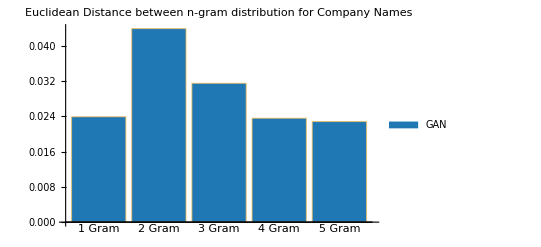

```mathematica
BarChart[companyGANDistance, ChartLegends->{"GAN"},ChartLabels->{"1 Gram","2 Gram","3 Gram","4 Gram","5 Gram"}, ChartStyle->{RGBColor["#1f78b4"]}, PlotLabel->"Euclidean Distance between n-gram distribution for Company Names"]
```

Comparison and Conclusion

The computed euclidean distance between the n-gram distributions for both the RNN and GAN model will help us make a better comparison between two model.

```mathematica
1. RNN vs GAN(Chemical Names)
```

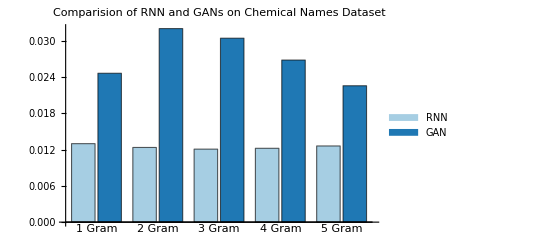

```mathematica
BarChart[Transpose@{ChemicalNamesDistancesRNN,chemicalDistanceGAN}, ]
```

-Graphics-

```mathematica
2. RNN vs GAN (Company Names)
```

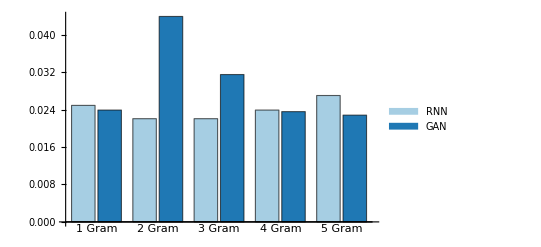

```mathematica
BarChart[Transpose@{CompanyNamesDistancesRNN,companyGANDistance}, ]
```

-Graphics-

From the above comparison, we can see that the GAN model’s for chemical names wasn’t too significant, however, for the company names dataset GAN’s performance was comparable and if not better (for 1,4 and 5 grams). This could be because the chemical names (8+ characters) were longer compared to company names (6 or less characters). We believe that further fine tuning and some architectural changes can improve the overall performance of the GAN model for both the datasets. In addition, the “Wolfram English Character-Level Language Model V1” was pretrained with training set consisting of 1.5 GB of text from old novels and news articles, which might have made it easier for the RNN model to learn the text features quickly while the GAN was trained from scratch and for fewer rounds. All in all, the GAN model’s performance even with shorter training on the same datasets is impressive.

## Complete project work

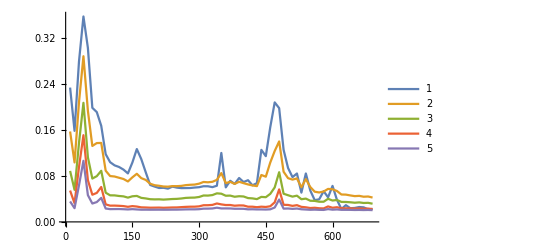
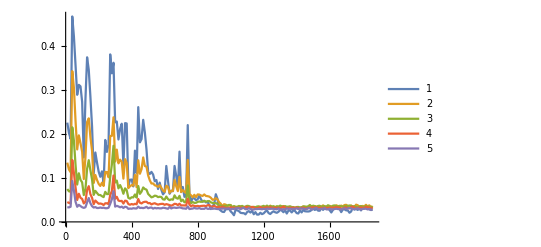
Performance Metric

Normalizing text
To compare the different model performances, we will be finding the euclidean distance of n-grams between text generated from two models. The initial step will be to remove special characters and diacritics from the real dataset. The following code accomplishes this goal by using a combination of StringReplace, ToLowerCase and Remove Diacritics functions to normalize the characters in the dataset.
normalizeText[s_] := ToLowerCase @ RemoveDiacritics @ StringReplace[s,
	{WordBoundary~~(WordCharacter..)~~".":>"",(*Remove "mr.","jr.",...*)
	"♂"|"♀"→"",(*Remove gender hints*)
	"-"|"-"|"'"→" ",(*Remove very rare characters*)
	DigitCharacter→"" ,(*Remove very rare characters*)
	"("|")" → "",(*Remove Brackets*)
	"%"|":" → "",(*Remove Colons and %*)
	"ʻ" |"‘"→  "",(*Remove other special characters*)
	"`"→"",
	" " → "",
	"="|"?"→"",
	"}"|"{"→ ""}
]

Computing n-grams
The next step is to create a lookup table for the different characters so that we can put them in their respective coordinates in the sparse array. The following code makes an association that maps characters and special tokens to an unique point.
characters = AssociationThread[
	Join[CharacterRange["a","z"], {" ", StartOfString, EndOfString}]
	→ Range[29]];
A function to compute n-grams is created which computes n-gram for a given wordlist and puts frequencies of each n-gram in a SparseArray. A sparse-array is chosen for faster computation for higher “n” in the n-grams.

computeNGrams[texts_, n_] := Block[{ngrams},
	ngrams = Flatten[
		Function[Partition[#, n, 1]] /@ 
		Function[Join[{StartOfString}, Characters[#], {EndOfString}]] /@ normalizeText[texts],
		1
	];
	(* Convert to indices *)
	ngrams = Map[Lookup[characters, #]&, ngrams];
	(* Counts *)
	ngrams = Normal[N @ Counts[ngrams] / Length[ngrams]];
	(* Fill SparseArray *)
	SparseArray[ngrams, Table[Length[characters],n]]
];

Euclidean Distance between n-gram distributions
We then compute the euclidean distance between the distributions of n-grams in the dataset and generated text. The findEuclideanDistance computes the euclidean distance between two n gram distributions. The DistancesofNgrams function takes the generator and the training dataset to find the euclidean distance between n-gram distributions (between generated and training dataset) where n goes from 1 to 5.
findEuclideanDistance[ngram1_,ngram2_]:= EuclideanDistance[Flatten@ngram1,Flatten@ngram2]

DistancesofNgrams[generator_, dataset_]:= Table[findEuclideanDistance[computeNGrams[generator@latentGeneration[1000],n], computeNGrams[dataset,n]],{n,1,5}]

Using this metric we will be able to compare the GAN model as well as the RNN model. In addition, we will be able to see how the euclidean distance converges as the GAN model is trained.


Training RNN Models
Import necessary data
Chemical Names

chemicalNames = EntityValue[EntityList["Chemical"],"Name"];
chemicalNames = Select[chemicalNames,StringMatchQ[#,CharacterRange["A","z"]..]&];

Company Names

dataset= Import["/Users/sumansigdel/Downloads/companies_sorted.csv"];
shortCompaniesList = Select[Flatten@dataset, StringLength[#] ≤6 &];
“A”→1,”)”→1,”.”→2,”$”→1,”;”→1,”Z”→1|>
">"→"","."→"",","→"","""→"","\n"→"","/"→"","&"→""

Functions for removing special characters.

normalizeText[s_] := ToLowerCase @ RemoveDiacritics @ StringReplace[s,
	{WordBoundary~~(WordCharacter..)~~".":>"",(*Remove "mr.","jr.",...*)
	"♂"|"♀"→"",(*Remove gender hints*)
	"-"|"-"|"'"→" ",(*Remove very rare characters*)
	DigitCharacter→"" ,(*Remove very rare characters*)
	"("|")" → "",(*Remove Brackets*)
	"%"|":" → "",(*Remove Colons and %*)
"ʻ" |"‘"→  "",
"`"→"",
" " → "",
"["|"]"→ "",
"="|"?"→"",
"}"|"{"→ "",
"\"→ "",
"^"|"`"→ "",
"_" → "",
"!"|"#"→ "",
")"|"$"→"",
";"→ "",">"→"","."→"",","→"","""→"","\n"→"","/"→"","&"→"","
"→ ""}];
Normalize all the data

shortCompanyNames = normalizeText@shortCompaniesList;
normalizedChemicalNames = normalizeText@chemicalNames;
Get the pretrained model
net=NetModel["Wolfram English Character-Level Language Model V1","TrainingNet"];
vocabulary=Characters["	
 !"#$%&'()*+,-./0123456789:;<=>?@ABCDEFGHIJKLMNOPQRSTUVWXYZ[\]^_`abcdefghijklmnopqrstuvwxyz{}é"];
net=NetReplacePart[net,"Input"→NetEncoder[{"Characters",{vocabulary,{StartOfString,EndOfString}→97}}]]
NetGraph[<>]
Training the pretrained model with Chemical names

Take[normalizedChemicalNames,20]
{"hydrogen","helium","deuterium","lithium","beryllium","boron","diamond","graphite","borane","methane","ammonia","ice","steam","water","neon","methyllithium","sodium","magnesium","acetylene","aluminum"}

chemicalResults=NetTrain[net,<|"Input"→normalizedChemicalNames|>,All,LossFunction→"Loss",MaxTrainingRounds→40];
Chemicalnet=NetReplacePart[net,"Input"→NetEncoder[{"Characters",{vocabulary,{StartOfString,EndOfString}→97}}]]
NetGraph[<>]
chemicalRNN = Export["ChemicalRNN.wlnet",Chemicalnet];
Chemicalnet = Import["/Users/sumansigdel/ChemicalRNN.wlnet"]
NetGraph[<>]
Chemicalnet=NetReplacePart[NetExtract[Chemicalnet,"predict"],{"Input"→NetEncoder[{"Characters",{vocabulary,EndOfString},"TargetLength"→1}],"Output"→NetDecoder[{"Class",Append[vocabulary,""]}]}]
NetChain[<>]
randomChemical[]:=With[{obj=NetStateObject[Chemicalnet]},StringJoin@NestWhileList[obj[Last[#],"RandomSample"]&,Sequence[{"",""},#=!={""}&,1,100]]];
newChemicals=Sort@Complement[Table[randomChemical[],5], normalizedChemicalNames]
{"dichloroglucinol","discadenylonitrile","phenoxyfluoramide","triphenylacetylene"}
characters1 = AssociationThread[
	Join[CharacterRange["a","z"], {StartOfString, EndOfString}]
	→ Range[28]];

computeNGrams[texts_, n_] := Block[{ngrams},
	ngrams = Flatten[
		Function[Partition[#, n, 1]] /@ 
		Function[Join[{StartOfString}, Characters[#], {EndOfString}]] /@ normalizeText[texts],
		1
	];
	(* Convert to indices *)
	ngrams = Map[Lookup[characters1, #]&, ngrams];
	(* Counts *)
	ngrams = Normal[N @ Counts[ngrams] / Length[ngrams]];
	(* Fill SparseArray *)
	SparseArray[ngrams, Table[Length[characters1],n]]
];

findEuclideanDistance[ngram1_,ngram2_]:= EuclideanDistance[Flatten@ngram1,Flatten@ngram2];
DistancesofNgrams[generator_, dataset_]:= Table[findEuclideanDistance[computeNGrams[generator@latentGeneration[500],n], computeNGrams[RandomChoice[dataset,500],n]],{n,1,5}];
DistanceofNgramsChemicals[dataset1_,dataset2_]:= Table[findEuclideanDistance[computeNGrams[dataset1],n], computeNGrams[RandomChoice[dataset2,500],n],{n,1,5}];
Import["/Users/sumansigdel/ChemicalRNN.wlnet"]
NetGraph[<>]
ChemicalNamesDistancesRNN= Table[findEuclideanDistance[computeNGrams[newChemicals,n], computeNGrams[normalizedChemicalNames,n]],{n,1,5}]
{0.0129824,0.0123536,0.0120765,0.0122143,0.0126008}
BarChart[ChemicalNamesDistancesRNN,ChartLabels→{"1 Gram","2 Gram","3 Gram","4 Gram","5 Gram"}, ChartLegends→{"RNN"},PlotLabel→"Euclidean Distance between n-gram distribution for Chemical Names",ChartStyle→{RGBColor["#a6cee3"]}]
-Graphics-

Training the pretrained model with Company Names
Max@StringLength@normalizedShortCompaniesList
6
CompanyNamesRNNnet=NetReplacePart[net,"Input"→NetEncoder[{"Characters",{vocabulary,{StartOfString,EndOfString}→97}}]]
NetGraph[<>]
CompanyNamesresults=NetTrain[CompanyNamesRNNnet,<|"Input"→normalizedShortCompaniesList|>,All,LossFunction→"Loss",MaxTrainingRounds→100]
"NetTrain Results"
"summary" | ,"," " ""batches:"41 " ""rounds:"1 " ""time:""3.3s" " ""examples/s:"400
"data" | ,"," " ""training examples:"10000 " ""processed examples:"1312 " ""skipped examples:"0
"method" | ,"," " ""ADAM""optimizer" " ""batch size"32"CPU"
"round" | ,"," " ""loss:"" — " " ""error:"" — "
 | 
"" | 
companyRNN = Import["/Users/sumansigdel/CompanyRNN3rd.wlnet"]
NetGraph[<>]
companyNamegenerator=NetReplacePart[NetExtract[companyRNN,"predict"],{"Input"→NetEncoder[{"Characters",{vocabulary,EndOfString},"TargetLength"→1}],"Output"→NetDecoder[{"Class",Append[vocabulary,""]}]}]


NetChain[<>]
randomGeneratedCompany[]:=With[{obj=NetStateObject[companyNamegenerator]},StringJoin@NestWhileList[obj[Last[#],"RandomSample"]&,Sequence[{"",""},#=!={""}&,1,100]]];
generatedCompany = Sort@Complement[Table[randomGeneratedCompany[],10000], normalizedShortCompaniesList];
NetTrain[gan,dataGenerator,TargetDevice→"GPU",BatchSize→$batchsize,TrainingUpdateSchedule→{"Discriminator","Discriminator","Generator"},MaxTrainingRounds→100000,
TrainingProgressFunction→{{Function@Block[{generator, ngramDistance},
generator=NetExtract[#Net,"Generator"];
ngramDistance =DistancesofNgrams[generator,normalizedChemicalNames];
Echo@ngramDistance;


],"Interval"→Quantity[10,"Rounds"]},

{
wssTrainingProgressFunction,
"Interval"→Quantity[10,"Rounds"]
}

},
TimeGoal→timeGoal
];
Table[findEuclideanDistance[computeNGrams[m,n], computeNGrams[SeedRandom[1234];RandomChoice[normalizedShortCompaniesList,5000],n]],{n,1,5}]
{0.021007,0.0169956,0.0143021,0.0154484,0.0184191}
Take[normalizedShortCompaniesList,10]
{"ibm","ey","att","pwc","citi","amazon","apple","oracle","nokia","hsbc"}
normalizedShortCompaniesList = normalizeText@Select[Flatten@dataset, StringLength[#] ≤6 &];
Take[normalizedShortCompaniesList,10]

{"ibm","us army","ey","walmart","att","pwc","infosys","deloitte","citi","us navy"}

Training the pretrained character level RNN on the company names dataset.
CompanyNamesnet=NetReplacePart[net,"Input"→NetEncoder[{"Characters",{vocabulary,{StartOfString,EndOfString}→97}}]]
CompanyNamesresults=NetTrain[CompanyNamesnet,<|"Input"→normalizedShortCompaniesList|>,All,LossFunction→"Loss",MaxTrainingRounds→100]
NetGraph[<>]
Upon running the RNN model, the following examples were produced and the euclidean distance is calculated as per the performance metric.
generatedCompany=Sort@Complement[Table[randomGeneratedCompany[],1000],normalizedShortCompaniesList];
Take[generatedCompany,10]
{"aamp","aasu","aceic","acmas","acolux","actain","acws","adayi","addpowar","adio"}
CompanyNamesDistancesRNN =Table[findEuclideanDistance[computeNGrams[generatedCompany,n], computeNGrams[SeedRandom[1234];RandomChoice[normalizedShortCompaniesList,1000],n]],{n,1,5}]

{0.0249101,0.0220684,0.0220686,0.0239113,0.027024}
BarChart[CompanyNamesDistancesRNN,ChartLabels→{"1 Gram","2 Gram","3 Gram","4 Gram","5 Gram"}, ChartLegends→{"RNN"},PlotLabel→"Euclidean Distance between n-gram distribution for Company Names",ChartStyle→{RGBColor["#a6cee3"]}]
-Graphics-

generated = {"sateco","soft","kiopote","rielli","grkc","mooch","valigus","celele","aws","amo","werlow","coptema","paletek","gip","sarmat","yoyeo","firmed","amaze","cism","cybergy","gum","shiptal","fph","octato","oep","lova","vhb","arcnip","ztopay","suprim","olangro","appnex","tcsc","poyea","avigers","sculames","fifi","mok","vaizen","dur","weadin","amic","careus","dssi","absis","thea","aukure","co","coaings","inexs","xelyos","isp","reflex","ipysec","frina","idea","of","prophl","meturem","lorvest","scht","temart","lxy","fort","rodo","chintech","taymob","ufeep","cusi","it","hieva","ezon","enexio","innod","unicon","aetom","argate","reloti","forix","greenox","acis","cer","noodkon","ska","vister","baltie","texia","aft","inbam","kim","floress","qsb","cridy","enmed","ame","webblev","sig","syz","energis","cilea","fishio","lomenan","sgi","gisi","vilvil","sgt","greyx","wece","itronics","blugt","ogw","sabamo","ssat","cosey","bellise","shapt","wermay","devre","weyz","chace","enelly","intrax","pre","facef","bbxt","grr","asa","sanow","penzig","symelity","ldg","kogul","nutory","intiva","newros","zusup","isna","avesys","houfood","rocead","cetb","genatek","ctc","upsus","citel","whr","com","robercon","katik","ttti","ce","cibi","novix","rolden","prolaude","tcl","winway","urbin","ofmax","highrs","ire","com","ama","stabit","alvere","wilight","afat","steeddank","wis","zoetzin","omnition","isba","novasup","exera","synars","eawash","sextras","dms","netlife","optimoy","aladi","artipa","mast","kona","arcyon","ace","met","agriut","csv","assi","aprimax","luml","fibs","intrams","dtm","vogogal","keimond","armi","iconx","dff","revo","onoop","glenzz","geomaisa","fisho","od","grupo","bamte","acclow","aretel","pr","revet","mdi","sa","macna","intaworx","lbc","ecolab","biovati","com","susa","strata","exonet","sutergy","atc","y","cld","acclic","sateb","shop","mark","bhg","irp","netex","spirice","nosa","setra","kti","lida","iob","vexbase","atariann","ferest","icc","cira","umbi","pst","weformax","curup","smolex","kyca","icco","yano","maf","shore","jiware","qelot","stech","designa","semcik","emcahx","mciti","nfuz","jaksom","dotooin","microsat","mesco","iqur","esa","paktech","kmkt","cardot","inexa","zot","acs","vcm","salcode","convaix","beifs","pnd","ieb","icon","aculifz","fmac","ingrapak","betav","kasoh","ilpi","intactor","forec","comse","certac","itfli","irecf","fibo","norner","mcog","skylab","opvoy","duna","gfml","sadah","altcon","magirem","cyg","vl","filoyou","wemco","chaz","endap","veac","eff","conff","vecto","serop","ari","bimba","tv","aplink","cajatah","optome","ssyd","divitno","wgr","lyga","am","enci","proferge","smans","fege","scdm","yobtel","versiros","txg","cactio","piram","usni","apcen","xunn","best","pertik","pagvage","bify","nideb","fosi","storweb","cnc","cybess","gosco","lafa","care","lynder","nuvicon","casthi","npco","harcprod","sapli","ubbc","frycp","uft","surdi","origu","sfaa","cls","kasanica","fri","biosigs","proxite","levisys","gmd","inovest","pfi","ittc","vetcus","sco","hasmaco","huch","idocs","alpo","duxneo","etrx","tcs","omnisys","pcd","dorcfr","cvf","tj","actorom","cali","primie","cees","lengweb","caadoc","catto","thende","imditi","mozo","jaga","blueit","crmst","theuro","jsa","psst","nidu","idi","smanh","imtr","uk","fitmic","ave","blue","perrint","mapy","inco","likkai","assi","berkam","edata","agg","zipher","wfl","creazimi","tiemark","tpg","cloudry","abibo","lcc","danry","dinctre","rumake","forcitap","fito","egan","sdri","kcce","digmont","feton","folmos","thodata","rdas","angua","alcole","aou","wtc","innovoty","fresh","nuvent","softtech","rai","ncgsa","aste","fridge","emeptis","cef","bory","kac","nyact","infoeco","hita","koyim","sfw","sodelit","arc","ld","hpdt","allantec","aks","isrd","cara","netreit","flamo","saf","pitilap","caracat","cognci","bds","symply","bookd","cepac","masa","twv","ll","nr","sehedi","lasc","usr","pft","clic","swic","sma","cryogate","estange","io","sad","comet","ng","give","secudot","igyn","joovo","surlcon","techfio","therit","attill","pageum","edrap","marven","sode","putch","permacap","meltis","experus","move","noolac","optiloom","senter","routaiq"};
Training GAN
Import dataset and Remove special characters.

dataset= Import["/Users/sumansigdel/Downloads/companies_sorted.csv"];
normalizeText[s_] := ToLowerCase @ RemoveDiacritics @ StringReplace[s,
	{WordBoundary~~(WordCharacter..)~~".":>"",(*Remove "mr.","jr.",...*)
	"♂"|"♀"→"",(*Remove gender hints*)
	"-"|"-"|"'"→" ",(*Remove very rare characters*)
	DigitCharacter→"" ,(*Remove very rare characters*)
	"("|")" → "",(*Remove Brackets*)
	"%"|":" → "",
"["|"]"→"",
"!"|"&"→"",
"/"|"+"→"",(*Remove Colons and %*)
"["|"]"→ "",
"\"→ "",
"^"|"`"→ "",
"_" → ""}];
shortCompaniesList = Select[Flatten@dataset, StringLength[#] ≤6 &];
shortCompaniesList = normalizeText@shortCompaniesList
{"ibm","ey","att","pwc","citi","amazon","apple","oracle","nokia","hsbc","google","nhs","boeing","cisco","target","shell","ups","pfizer","nestle","dell","gsk","sap","abb","bp","dhl","td","ge","ubs","sanofi","sodexo","kpmg","orange","adp","abbott","roche","macy s","avon","cgi","atos","csc","merck",61850,"wati","fiasa","essi","tohero","popvox","aigent","spch","","draad","caga","unison","empsol","pert","mzv","shadow","da","rsid","nxgn","vynd","kuva","kxu","unimat","weko","gne","ncrep","kanfit","thunis","adeya","sawea","idezi","ecoad","vastly","mcro","legend","subopp","minero","obo","gendex","torq","cirqit","risch"}
"(""Expression size: ""2.5"" MB)" | "|" | " | "" | "" | "" | "" | "
normalizedShortCompaniesList =normalizeText@Select[shortCompaniesList,StringMatchQ[#,CharacterRange["A","z"]..]&];
normalizedShortCompaniesList // Length
59275
normalizedShortCompaniesList = Take[normalizedShortCompaniesList,10000];

Counts@Flatten@Characters@normalizedShortCompaniesList
<|"i"→3149,"b"→1277,"m"→2217,"e"→3701,"y"→504,"a"→4759,"t"→2283,"p"→1593,"w"→404,"c"→3129,"z"→261,"o"→2545,"n"→2283,"l"→1562,"r"→2223,"k"→755,"h"→828,"s"→3482,"g"→1040,"u"→1138,"f"→911,"d"→1491,"x"→452,"v"→768,"j"→229,"q"→147|>
GAN Model Architecture for company names
Hyperparameters
$jensen=True;(*Jensen or Wasserstein*)
$numposfeatures=0;
$numlatent=10;(*Dimension of the latent space*)
$numhiddens=128;(*CNN Hidden Layers*)
$depth=2;(*Number of CNN*)
$kernelSize=5; (*Look at five grams of characters*)
$batchsize=32;
$discriminatorTerminalTokensQ=True;
$generatorTerminalTokensQ=True;

counts=Counts[StringLength/@normalizedShortCompaniesList];(*We will use this to generate a realistic length*)
characters=Union[Flatten@Characters@normalizedShortCompaniesList];
characters2=If[$discriminatorTerminalTokensQ,Join[characters,{StartOfString,EndOfString}],characters];
counts
<|3→2989,2→333,4→2236,6→2352,5→2088,1→2|>

netpreproc=NetEncoder[{"Characters",characters2,"IgnoreCase"→True}];
nonlinearityGenerator=ElementwiseLayer[If[#>0,#,0.2*#]&];
nonlinearityDiscriminator=ElementwiseLayer[If[#>0,#,0.2*#]&];
batchnorm=BatchNormalizationLayer[(*"Scaling"→None,"Biases"→None*)"Scaling"→1,"Biases"→0,"Interleaving"→True,LearningRateMultipliers→{"Scaling"→0,"Biases"→0,_→1}];
instancenorm=NormalizationLayer[1,"Scaling"→None,"Biases"→None];
normalizationGenerator=batchnorm;
normalizationDiscriminator=batchnorm;
convolutionBlock[n_,args___]:=NetChain[{ConvolutionLayer[n,{$kernelSize},"Stride"→{1},PaddingSize→(($kernelSize-1)/2),"Interleaving"→True,args],normalizationDiscriminator,nonlinearityDiscriminator,DropoutLayer[]}];

Discriminator Model

textDiscriminator=NetChain[<|(*Preprocessing:only keep the maximum values*)"keep max only"→NetGraph[{AggregationLayer[Max,-1],ThreadingLayer[If[#1≥#2-1.*^-7,#1,0]&,-1]},{{NetPort["Input"],1}→2}],Sequence@@Table["conv."<>ToString[i]→convolutionBlock[$numhiddens],{i,$depth}],"aggregate"→AggregationLayer[Mean,1],"dropout"→DropoutLayer[],"classify"→LinearLayer["Real","Weights"→0,"Biases"→None],If[$jensen,"logit"→LogisticSigmoid,Nothing]|>,"Input"→{"Varying",Length[characters2]}];
textDiscriminator
NetChain[<>]

Generator Model

textGenerator=NetChain[<|If[$generatorTerminalTokensQ,(*Append/Prepend EOS/SOS feature vectors*)"add eos/sos latent"→NetGraph[{ArrayLayer[],AppendLayer[],ArrayLayer[],PrependLayer[]},{{NetPort["Input"],1}→2,{2,3}→4}],Nothing],(*Core deep net*)Sequence@@Table["conv."<>ToString[i]→convolutionBlock[$numhiddens],{i,$depth}],If[$generatorTerminalTokensQ,(*Remove EOS/SOS high level features*)"remove eos/sos prediction"→NetChain[{SequenceRestLayer[],SequenceMostLayer[]}],Nothing],(*Classifier (of characters)*)"classify"→NetMapOperator@LinearLayer[Length[characters](*,"Weights"→0*)],"squash"→SoftmaxLayer[],If[$discriminatorTerminalTokensQ,"add eos/sos onehot proba"→NetGraph[{(*Catenate zero proba for EOS/SOS inside the generated text*)PaddingLayer[{{0,0},{0,2}}],(*Append/Prepend proba of 1 for EOS/SOS at the end/beginning of the generated text (to be in accordance with the discriminator)*)ArrayLayer["Array"→UnitVector[Length[characters2],Length[characters2]-1],LearningRateMultipliers→None],PrependLayer[],ArrayLayer["Array"→UnitVector[Length[characters2],Length[characters2]],LearningRateMultipliers→None],AppendLayer[]},{{1,2}→3,{3,4}→5}],Nothing]|>,"Input"→{"n",$numlatent},"Output"→With[{netpostproc=NetDecoder[netpreproc]},(*Capitalize the decoded (lower-case) text*)NetDecoder[{"Function",Function[StringReplace[netpostproc[#],WordBoundary~~c:WordCharacter:>ToUpperCase[c]]]}]]]
NetChain[<>]

Random one hot encoding, Latent Generation and Sample generation

(*Generation of latent random*)
latentGeneration[batchSize_]:=Table[Block[{len=Max[3,RandomChoice[Values[counts]→Keys[counts]]]},NumericArray[#,"Real32"]&@Clip[RandomVariate[NormalDistribution[],{len,$numlatent}],{-1,1}]],batchSize];
randomizeOnehot[onehot_]:=If[$discriminatorTerminalTokensQ,Join[{First@onehot},Map[#*Clip[RandomVariate[NormalDistribution[0.8,0.1]],{0.55,1}]&,Rest@Most@onehot],{Last@onehot}],Map[#*Clip[RandomVariate[NormalDistribution[0.8,0.1]],{0.55,1}]&,onehot]];
sampleGeneration[batchSize_]:=Block[{s,onehot},s=RandomSample[normalizedShortCompaniesList,batchSize];
onehot=UnitVectorLayer[Length[characters2],"Input"→{Automatic}][netpreproc[s]];
NumericArray[#,"Real32"]&/@Map[randomizeOnehot,onehot]];

GAN Model

dataGenerator={Function[<|"Sample"→sampleGeneration[#BatchSize],"Latent"→latentGeneration[#BatchSize]|>],"RoundLength"→Length[normalizedShortCompaniesList]};
companyGAN=NetGANOperator[{textGenerator,textDiscriminator}]
NetGANOperator[<>]
normalizedShortCompaniesList
{"ibm","ey","pwc","citi","amazon","apple","oracle","nokia","hsbc","google","nhs","boeing","cisco","target","shell","ups","pfizer","nestle","dell","gsk","sap","abb","bp","dhl","td","ge","ubs","sanofi","sodexo","kpmg","orange","adp","abbott","roche","avon","cgi","atos","csc","merck","kpmg","axa",58571,"zamo","wati","fiasa","essi","tohero","popvox","aigent","spch","draad","caga","unison","empsol","pert","mzv","shadow","da","rsid","nxgn","vynd","kuva","kxu","unimat","weko","gne","ncrep","kanfit","thunis","adeya","sawea","idezi","ecoad","vastly","mcro","legend","subopp","minero","obo","gendex","torq","cirqit","risch"}
"(""Expression size: ""2.3"" MB)" | "|" | " | "" | "" | "" | "" | "
Importing model trained on AWS instance

companyGAN3rd = Import["/Users/sumansigdel/CompanyGAN3rd.wlnet"]
NetGANOperator[<>]
companyGEN3rd = NetExtract[companyGAN3rd,"Generator"]
NetChain[<>]
latentGeneration[1]
{NumericArray[…]}
Counts@Flatten@Characters@normalizedShortCompaniesList
<|"i"→3154,"b"→1270,"m"→2221,"e"→3717,"y"→506,"p"→1599,"w"→406,"c"→3139,"t"→2290,"a"→4768,"z"→262,"o"→2552,"n"→2292,"l"→1570,"r"→2225,"k"→757,"h"→829,"s"→3485,"g"→1044,"u"→1149,"f"→916,"d"→1481,"x"→454,"v"→767,"j"→224,"q"→147|>
DistancesofNgrams[comapnyGEN3rd ,normalizedShortCompaniesList]
{0.0220411,0.042386,0.0316547,0.0222756,0.0204714}
m = latentGeneration[100];

companyGEN3rd@m 
{"Nudeoa","Censm","Rfgg","Unh","Csocso","Ans","Cccmm","Acac","Rsime","Udefu","Nenvam","Sfdii","Darii","Blba","Idefa","Ons","Grrsvh","Celn","Vsfteg","Aacn","Srmg","Oknha","Budude","Sasipi","Elleps","Dfre","Bua","Grdk","Mera","Obt","Sgoo","Iderv","Ddr","Mme","Rret","Stl","Cos","Mgras","Gre","Uude","Gmabms","Neac","Kham","Rkha","Iteg","Avhvts","Lsa","Oposop","Niii","Hscb","Mmam","Vde","Eds","Lrr","Lppne","Deins","Cams","Cabmha","Acebnd","Hsaupp","Mmm","Ablu","Ahcabb","Men","Der","Dsandu","Lenac","Srs","Lepb","Itotp","Aaso","Anicsl","Anu","Ttoins","Fgvam","Sirefs","Pppo","Dsg","Rotets","Uunsa","Mgmm","Ramr","Pnko","Lolnaa","Mabdf","Aafneo","Cbdreh","Mel","Mmada","Meras","Hcva","Lero","Abulu","Tsos","Aramra","Cam","Tso","Ama","Roamca","Bme"}
companylogcsv = Import["/Users/sumansigdel/DistanceLogAWSCOMPANY.csv"];
columns=Transpose@Rest@companylogcsv;
rounds=First[columns];
ListLinePlot[Map[Transpose[{rounds,#}]&,Rest[columns]], PlotRange→All, PlotLegends→{1,2,3,4,5}]
-Graphics-

companyGAN = Import["/Users/sumansigdel/CompanyGAN3rd.wlnet"]
NetGANOperator[<>]
latentGeneration[batchSize_]:=Table[Block[{len=Max[3,RandomChoice[Values[counts]→Keys[counts]]]},NumericArray[#,"Real32"]&@Clip[RandomVariate[NormalDistribution[],{len,10}],{-1,1}]],batchSize];
companyGenerator= NetExtract[companyGAN,"Generator"];
companyGenerator@latentGeneration[10]
{"Pipsf","Sins","Gsacs","Pegvg","Amgia","Rapen","Rvdi","Rfd","Meme","Abm"}
companyGANDistance =DistancesofNgrams[companyGenerator, normalizedShortCompaniesList]
{0.0239126,0.0439251,0.0315068,0.0235774,0.0228289}
BarChart[companyGANDistance, ChartLegends→{"GAN"},ChartLabels→{"1 Gram","2 Gram","3 Gram","4 Gram","5 Gram"}, ChartStyle→{RGBColor["#1f78b4"]}, PlotLabel→"Euclidean Distance between n-gram distribution for Company Names"]
-Graphics-
Training GAN on chemical names
(***********************************)(*Hyper-parameters (to be tuned!)*)(***********************************)
$jensen=True;(*Jensen or Wasserstein*)
$numposfeatures=0;
$numlatent=16;(*Dimension of the latent space*)$numhiddens=128;(*CNN Hidden Layers*)$depth=2;(*Number of CNN*)$kernelSize=5; (*Look at five grams of characters*)
$batchsize=32;
$discriminatorTerminalTokensQ=True;
$generatorTerminalTokensQ=True;
$updateDiscriminator=1;
(*Other variables*)
ngramInfo = {};
(*Use a folder name to dump intermediate results into it*)
$SAVEDIR="/Users/sumansigdel/documents/ChemicalNames";
$device="CPU";

normalizeText[s_] := ToLowerCase @ RemoveDiacritics @ StringReplace[s,
	{WordBoundary~~(WordCharacter..)~~".":>"",(*Remove "mr.","jr.",...*)
	"♂"|"♀"→"",(*Remove gender hints*)
	"-"|"-"|"'"→" ",(*Remove very rare characters*)
	DigitCharacter→"" ,(*Remove very rare characters*)
	"("|")" → "",(*Remove Brackets*)
	"%"|":" → "",
"["|"]"→""}(*Remove Colons and %*)];

c = EntityValue[EntityList["Chemical"],"Name"];
chemicalNames = Select[c,StringMatchQ[#,CharacterRange["A","z"]..]&];
normalizedChemicalNames = normalizeText@chemicalNames;


counts=Counts[StringLength/@normalizedChemicalNames];(*We will use this to generate a realistic length*)
characters=Union[Flatten@Characters@normalizedChemicalNames];
characters2=If[$discriminatorTerminalTokensQ,Join[characters,{StartOfString,EndOfString}],characters];

netpreproc=NetEncoder[{"Characters",characters2,"IgnoreCase"→True}];

nonlinearityGenerator=ElementwiseLayer[If[#>0,#,0.2*#]&];
nonlinearityDiscriminator=ElementwiseLayer[If[#>0,#,0.2*#]&];

batchnorm=BatchNormalizationLayer[(*"Scaling"→None,"Biases"→None*)"Scaling"→1,"Biases"→0,"Interleaving"→True,LearningRateMultipliers→{"Scaling"→0,"Biases"→0,_→1}];
instancenorm=NormalizationLayer[1,"Scaling"→None,"Biases"→None];
normalizationGenerator=batchnorm;
normalizationDiscriminator=batchnorm;
convolutionBlock[n_,args___]:=NetChain[{ConvolutionLayer[n,{$kernelSize},"Stride"→{1},PaddingSize→(($kernelSize-1)/2),"Interleaving"→True,args],normalizationDiscriminator,nonlinearityDiscriminator,DropoutLayer[]}];
textDiscriminator=NetChain[<|(*Preprocessing:only keep the maximum values*)"keep max only"→NetGraph[{AggregationLayer[Max,-1],ThreadingLayer[If[#1≥#2-1.*^-7,#1,0]&,-1]},{{NetPort["Input"],1}→2}],Sequence@@Table["conv."<>ToString[i]→convolutionBlock[$numhiddens],{i,$depth}],"aggregate"→AggregationLayer[Mean,1],"dropout"→DropoutLayer[],"classify"→LinearLayer["Real","Weights"→0,"Biases"→None],If[$jensen,"logit"→LogisticSigmoid,Nothing]|>,"Input"→{"Varying",Length[characters2]}];
textGenerator=NetChain[<|If[$generatorTerminalTokensQ,(*Append/Prepend EOS/SOS feature vectors*)"add eos/sos latent"→NetGraph[{ArrayLayer[],AppendLayer[],ArrayLayer[],PrependLayer[]},{{NetPort["Input"],1}→2,{2,3}→4}],Nothing],(*Core deep net*)Sequence@@Table["conv."<>ToString[i]→convolutionBlock[$numhiddens],{i,$depth}],If[$generatorTerminalTokensQ,(*Remove EOS/SOS high level features*)"remove eos/sos prediction"→NetChain[{SequenceRestLayer[],SequenceMostLayer[]}],Nothing],(*Classifier (of characters)*)"classify"→NetMapOperator@LinearLayer[Length[characters](*,"Weights"→0*)],"squash"→SoftmaxLayer[],If[$discriminatorTerminalTokensQ,"add eos/sos onehot proba"→NetGraph[{(*Catenate zero proba for EOS/SOS inside the generated text*)PaddingLayer[{{0,0},{0,2}}],(*Append/Prepend proba of 1 for EOS/SOS at the end/beginning of the generated text (to be in accordance with the discriminator)*)ArrayLayer["Array"→UnitVector[Length[characters2],Length[characters2]-1],LearningRateMultipliers→None],PrependLayer[],ArrayLayer["Array"→UnitVector[Length[characters2],Length[characters2]],LearningRateMultipliers→None],AppendLayer[]},{{1,2}→3,{3,4}→5}],Nothing]|>,"Input"→{"n",$numlatent},"Output"→With[{netpostproc=NetDecoder[netpreproc]},(*Capitalize the decoded (lower-case) text*)NetDecoder[{"Function",Function[StringReplace[netpostproc[#],WordBoundary~~c:WordCharacter:>ToUpperCase[c]]]}]]];
textGenerator
NetChain[<>]
N-gram Functions
characters1 = AssociationThread[
	Join[CharacterRange["a","z"], {StartOfString, EndOfString}]
	→ Range[28]];

computeNGrams[texts_, n_] := Block[{ngrams},
	ngrams = Flatten[
		Function[Partition[#, n, 1]] /@ 
		Function[Join[{StartOfString}, Characters[#], {EndOfString}]] /@ normalizeText[texts],
		1
	];
	(* Convert to indices *)
	ngrams = Map[Lookup[characters1, #]&, ngrams];
	(* Counts *)
	ngrams = Normal[N @ Counts[ngrams] / Length[ngrams]];
	(* Fill SparseArray *)
	SparseArray[ngrams, Table[Length[characters1],n]]
];

findEuclideanDistance[ngram1_,ngram2_]:= EuclideanDistance[Flatten@ngram1,Flatten@ngram2];
DistancesofNgrams[generator_, dataset_]:= Table[findEuclideanDistance[computeNGrams[generator@latentGeneration[Length@dataset],n], computeNGrams[SeedRandom[1234];RandomChoice[dataset,4000],n]],{n,1,5}];

(*Generation of latent random*)
latentGeneration[batchSize_]:=Table[Block[{len=Max[3,RandomChoice[Values[counts]→Keys[counts]]]},NumericArray[#,"Real32"]&@Clip[RandomVariate[NormalDistribution[],{len,$numlatent}],{-1,1}]],batchSize];
randomizeOnehot[onehot_]:=If[$discriminatorTerminalTokensQ,Join[{First@onehot},Map[#*Clip[RandomVariate[NormalDistribution[0.8,0.1]],{0.55,1}]&,Rest@Most@onehot],{Last@onehot}],Map[#*Clip[RandomVariate[NormalDistribution[0.8,0.1]],{0.55,1}]&,onehot]];
sampleGeneration[batchSize_]:=Block[{s,onehot},s=RandomSample[normalizedChemicalNames,batchSize];
onehot=UnitVectorLayer[Length[characters2],"Input"→{Automatic}][netpreproc[s]];
NumericArray[#,"Real32"]&/@Map[randomizeOnehot,onehot]];
dataGenerator={Function[<|"Sample"→sampleGeneration[#BatchSize],"Latent"→latentGeneration[#BatchSize]|>],"RoundLength"→Length[normalizedChemicalNames]};

gan=NetGANOperator[{textGenerator,textDiscriminator}]
NetGANOperator[<>]
1. Chemical Names
The same dataset of chemical names was used to train the following GAN.

chemicalGAN = Import["/Users/sumansigdel/ChemicalGAN.wlnet"]
NetGANOperator[<>]

We will now extract the generator from the GAN model and feed the latent random given by the latent generation function.

latentGeneration[batchSize_]:=Table[Block[{len=Max[3,RandomChoice[Values[counts]→Keys[counts]]]},NumericArray[#,"Real32"]&@Clip[RandomVariate[NormalDistribution[],{len,16}],{-1,1}]],batchSize];
chemicalGenerator = NetExtract[chemicalGAN,"Generator"];

Here are 10 chemical names generated by the GAN.

chemicalGenerator@latentGeneration[10]
{"Cephouromonazine","Cidenazine","Deropylltertine","Tramltne","Dinoamoldoxol","Metrexol","Flophabetrone","Poribeazene","Sulothlariyline","Macerminezone"}

We now use the performance metric with the chemical names and plot a bar chart. 

chemicalDistanceGAN = DistancesofNgrams[chemicalGenerator, normalizedChemicalNames]
{0.024628,0.0320187,0.0304281,0.0268123,0.0225618}
BarChart[chemicalGANDistance, ChartLegends→{"GAN"},ChartLabels→{"1 Gram","2 Gram","3 Gram","4 Gram","5 Gram"}, PlotLabel→"Euclidean Distance between n-gram distribution for Chemical Names",ChartStyle→{RGBColor["#1f78b4"]}]
-Graphics-

columns=Transpose@Rest@csv;
rounds=First[columns]
ListLinePlot[Map[Transpose[{rounds,#}]&,Rest[columns]], PlotRange→All, PlotLegends→{1,2,3,4,5}]
-Graphics-

Comparison and Conclusion
The computed euclidean distance between the n-gram distributions for both the RNN and GAN model will help us make a better comparison between two model.
1. RNN vs GAN(Chemical Names)
BarChart[Transpose@{ChemicalNamesDistancesRNN,chemicalDistanceGAN}, ChartLayout->"Grouped",ChartStyle→{RGBColor["#a6cee3"],RGBColor["#1f78b4"]},ChartLegends→{"RNN", "GAN"}, ChartLabels→{{"1 Gram","2 Gram","3 Gram","4 Gram","5 Gram"},None},PlotLabel→"Comparision of RNN and GANs on Chemical Names Dataset"]
-Graphics-

Grid[Partition[chemicalGenerator@latentGeneration[25],5], Frame→ True]

"Aephidtol" | "Amodaomite" | "Limlythine" | "Prise" | "Penomodon"
"Oloyllone" | "Poropyrane" | "Imenyltaol" | "Dlinosfon" | "Birysdade"
"Sallthllne" | "Staroprine" | "Cidrhoin" | "Cylthrzine" | "Ioulninenne"
"Phamburin" | "Flagltoe" | "Letrlornin" | "Elonentail" | "Dlaton"
"Etyadone" | "Adofamidine" | "Lcopyrphan" | "Olbenylpane" | "Ogetosil"

2. RNN vs GAN (Company Names)
BarChart[Transpose@{CompanyNamesDistancesRNN,companyGANDistance}, ChartLayout->"Grouped", ChartStyle→{RGBColor["#a6cee3"],RGBColor["#1f78b4"]}, ChartLegends→{"RNN", "GAN"},ChartLabels→{{"1 Gram","2 Gram","3 Gram","4 Gram","5 Gram"},None}]
-Graphics-

### Text Interpolation

```mathematica
chemicalGenerator = NetExtract[chemicalGAN,"Generator"];
```

```mathematica
p1 = latentGeneration[100];
```

```mathematica
p2 = latentGeneration[100];
```

```mathematica
p1Norm = Normal@p1;
p2Norm = Normal@p2;
```

```mathematica
interpolate[p1_,p2_]:=Table[(1.0-n)*p1+n*p2,{n,0,1,0.1}];
```

```mathematica
interpolate[#[[1]],#[[2]]]&/@Transpose@{p1Norm,p2Norm};
```

```mathematica
NumericArray[#,"Real32"]&/@interpolate[#[[1]],#[[2]]]&/@Transpose@{p1Norm,p2Norm};
```

```mathematica
m = chemicalGenerator[#]&/@%;
```

```mathematica
m  =Join[#,Reverse[#]]&/@m;
```

```mathematica
chemicalGenerator@p1
```

{Methylpaol,Closepreie}

```mathematica
chemicalGenerator@p2
```

{Mietoetayl,Amlonatine}

```mathematica
gif = ListAnimate[Multicolumn[#, Frame-> All]&/@Transpose@m]
```

## Keywords

Deep Learning

Generative Adversarial Networks

Text Generation

## Acknowledgment

Mentor: Tuseeta Banerjee

Thanks to Jerome Louradaur for guidance and initial GAN code.

## References

( Murgue T., de la Higuera C. (2004) Distances between Distributions: Comparing Language Models. In: Fred A., Caelli T.M., Duin R.P.W., Campilho A.C., de Ridder D. (eds) Structural, Syntactic, and Statistical Pattern Recognition. SSPR /SPR 2004. Lecture Notes in Computer Science, vol 3138. Springer, Berlin, Heidelberg)